# Gamma matrices, Schwinger-Dyson equations, and the SYK model

Abdel Elabd, June 2023
Following:
- https://www.youtube.com/watch?v=sU-_3BTftrY
- https://arxiv.org/abs/1711.08482
- https://arxiv.org/abs/1806.06840

#### First, load test coefficients

```mathematica
SeedRandom[0];
ℕ=14;
Nc = ℕ/2;

js = ArrayReshape[Import["C:\\Users\\abdel\\OneDrive\\Documents\\Gustavo Turiaci\\My Notes\\SYK and Consecutive-Level Spacings\\test_coefficients_K7_J4_q4.csv"], {ℕ, ℕ, ℕ, ℕ}];
js[[1,1,1]]
```

{0.329955,0.074847,0.183067,0.419145,0.349315,-0.182794,0.177708,-0.0283104,-0.0193065,0.0767999,0.0269425,0.272013,0.142347,0.0227586}

## 1. Define fermions

The starting point is that bosons commute and fermions anticommute (the latter having something to do with the Dirac equation, but we won’t get into that). We state here without proof that, to define our fermions, the simply must satisfy the Clifford algebra:
(1)         

Define          
 (2)         {c_i,c_j^†}==δ_ij

The algebra in (2) is equivalent to the algebra in (1), and also defines the canonical anticommutation relations for fermionic modes. So we interpret  as fermionic modes of a field.

We will work backwards, first defining the  operators that satisfy the algebra in (2); from those we can extract the  operators that satisfy (1), i.e. our fermions.

### a. Define fermionic modes

```mathematica
cr = {{0, 1}, {0, 0}}; 
an ={{0, 0}, {1, 0}};
id = IdentityMatrix[2];
id2 = {{-1, 0}, {0, 1}};
c[n_] := SparseArray[KroneckerProduct @@ (Table[id, {n-1}]~Join~{cr}~Join~Table[id2,{Nc-n}])]
cd[n_] := SparseArray[KroneckerProduct @@ (Table[id, {n-1}]~Join~{an}~Join~Table[id2,{Nc-n}])]
```

Check that these fermionic modes indeed satisfy the algebra in (2):

```mathematica
c[1].c[1]+c[1].c[1] //MatrixForm;
c[1].c[2]+c[2].c[1] //MatrixForm;
cd[1].cd[1]+cd[1].cd[1] //MatrixForm;
cd[1].cd[2]+cd[2].cd[1] //MatrixForm;
c[1].cd[1]+cd[1].c[1]//MatrixForm;
c[1].cd[2]+cd[2].c[1]//MatrixForm;
```

#### Notes from meeting:

,   . That is what’s happening above, reproduce analytically. If the different 2x2 blocks commuted, you would only need parentheses/2, but since they anticommute you need to multiply them by , which (in 2D) is like the identity matrix but with the first element flipped in sign, hence the anticommutation.  
Note: ,

### b. Define fermions

Now we can find . Since each one is expensive to compute and will be called upon many times, it’s more efficient to precompute a look-up table for the first K states of both  and .

```mathematica
Do[ψ[n]=1/(√2)(c[n]+cd[n]), {n,Nc}];
Do[ψ[Nc+n]=1/(√2)(-I c[n]+I cd[n]), {n, Nc}];
```

Don’t read too closely into the specific locations of the precomputed values. Analytically, there’s no relation - this is just a simple and efficient way to allocate the precomputed values of  to a lookup-table.

#### Check fermions satisfy algebra

```mathematica
ψ[1].ψ[1]+ψ[1].ψ[1]//MatrixForm;
ψ[1].ψ[3]+ψ[3].ψ[1]//MatrixForm;
```

## 2. Defining the Hamiltonian

Precompute the inner-product of every pair of fermions.

```mathematica
Do[ψ2[i1,i2]=ψ[i1].ψ[i2], {i1, ℕ}, {i2,i1+1,ℕ}]
```

(6)

Load coupling constants

```mathematica
q4=4;
𝔍4= 4;
js[[1,1,1]]
```

{0.329955,0.074847,0.183067,0.419145,0.349315,-0.182794,0.177708,-0.0283104,-0.0193065,0.0767999,0.0269425,0.272013,0.142347,0.0227586}

Precompute quadwise inner products.

```mathematica
Dynamic[{i1,i2,i3,i4}]
Do[ψ4[i1,i2,i3,i4] = ψ2[i1,i2].ψ2[i3,i4], {i1, ℕ}, {i2, i1+1, ℕ}, {i3, i2+1, ℕ}, {i4, i3+1, ℕ}]//Timing
```

{0.03125,Null}

Compute Hamiltonian

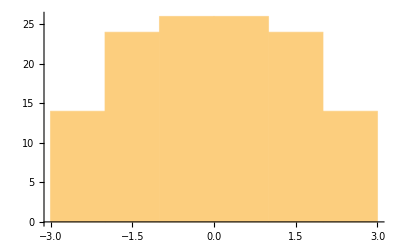

```mathematica
H4 = I^(q4/2) Sum[js[[i1,i2,i3,i4]] ψ4[i1, i2, i3, i4], {i1, ℕ}, {i2, i1+1, ℕ}, {i3, i2+1, ℕ}, {i4, i3+1, ℕ}]//Normal;
iv4 = H4//N//Eigenvalues//Sort;
iv4//Histogram
```

Looks like it’s approaching a semicircle distribution, but in the video he says it’s not for some reason.

```mathematica
iv4
```

{-2.71373,-2.71373,-2.50615,-2.50615,-2.39194,-2.39194,-2.28531,-2.28531,-2.22672,-2.22672,-2.10895,-2.10895,-2.06858,-2.06858,-1.94908,-1.94908,-1.9298,-1.9298,-1.87834,-1.87834,-1.75335,-1.75335,-1.63393,-1.63393,-1.53065,-1.53065,-1.44723,-1.44723,-1.36958,-1.36958,-1.33619,-1.33619,-1.24297,-1.24297,-1.11626,-1.11626,-1.06549,-1.06549,-0.928003,-0.928003,-0.8842,-0.8842,-0.817234,-0.817234,-0.764432,-0.764432,-0.588258,-0.588258,-0.534022,-0.534022,-0.43035,-0.43035,-0.413934,-0.413934,-0.352493,-0.352493,-0.299329,-0.299329,-0.196639,-0.196639,-0.106333,-0.106333,-0.00690898,-0.00690898,0.0973249,0.0973249,0.149299,0.149299,0.197229,0.197229,0.274499,0.274499,0.334136,0.334136,0.391627,0.391627,0.536499,0.536499,0.662785,0.662785,0.705645,0.705645,0.739608,0.739608,0.850821,0.850821,0.895937,0.895937,0.942459,0.942459,1.00388,1.00388,1.12887,1.12887,1.16353,1.16353,1.25367,1.25367,1.32979,1.32979,1.43523,1.43523,1.45474,1.45474,1.53793,1.53793,1.69638,1.69638,1.74684,1.74684,1.84989,1.84989,1.94402,1.94402,2.00201,2.00201,2.15727,2.15727,2.24236,2.24236,2.29389,2.29389,2.52411,2.52411,2.64177,2.64177,2.69235,2.69235}